```mathematica
(*Likelihood*)
sigmix=0.5;
L=MixtureDistribution[{1,1},{NormalDistribution[m1,sigmix],NormalDistribution[-m1,sigmix]}];lik[x_,m_]:=PDF[L,x]/.m1->m
```

```mathematica
Log[lik[D0,mu]]//CForm
```

Log(0.3989422804014327/Power(E,2.*Power(D0 - mu,2)) + 
    0.3989422804014327/Power(E,2.*Power(D0 + mu,2)))

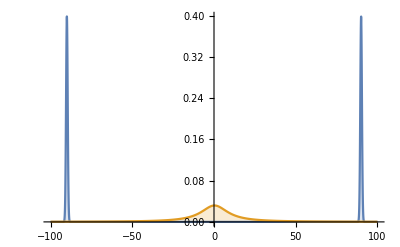

```mathematica
Data=90;
muhyp=0.3;
sighyp=10;
Plot[{lik[Data,μ],PDF[CauchyDistribution[muhyp,sighyp],μ]},{μ,-100,100},Filling->Axis, PlotRange->All]
```

```mathematica
Data=90;
muhyp=0.3;
sighyp=10;
lik[Data,μ]PDF[CauchyDistribution[muhyp,sighyp],μ]//FullSimplify
```

(ⅇ^((-360.-2. μ) μ) (3.4131341681×10^-7036+3.4131341681×10^-7036 ⅇ^(720. μ)))/(100.09+(-0.6+μ) μ)

```mathematica
Z=NIntegrate[lik[Data,μ]PDF[CauchyDistribution[muhyp,sighyp],μ],{μ, -Infinity,Infinity}]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

0.

```mathematica
logZ=-7.8706264693;(*From DNest*)
logZ=-7.86375197565;
logZ=-7.85655991677;
Z=Exp[logZ]
```

0.000387204

```mathematica
post[mu_]:=(lik[Data,mu]PDF[CauchyDistribution[muhyp,sighyp],mu])/Z
```

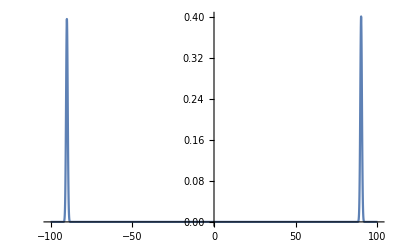

```mathematica
Plot[post[μ],{μ,-100,100},PlotRange->All]
```

```mathematica
NIntegrate[post[μ],{μ,-100,100}]
```

1.00265